```mathematica
$Assumptions={_∈Reals,-1<v<1,-L<x0<L};
```

```mathematica
Phif0[x_,t_]=Abs[x]/2;
w=ArcTanh[-v];
(Λ={{Cosh[w],-Sinh[w]},{-Sinh[w],Cosh[w]}})//MatrixForm;
boosted=Λ.{t,x-x0};
tprime=boosted[[1]];
xprime=boosted[[2]];
Phifzv[x0_,v_,x_,t_]=Phif0[xprime,tprime]//FullSimplify
Pifzv[x0_,v_,x_,t_]=D[Phifzv[x0,v,x,t],t]//FullSimplify
Psifzv[x0_,v_,x_,t_]=D[Phifzv[x0,v,x,t],x]//FullSimplify
```

Abs[t v+x-x0]/(2 √(1-v^2))

(v Sign[t v+x-x0])/(2 √(1-v^2))

Sign[t v+x-x0]/(2 √(1-v^2))

```mathematica
Φ[x0_,v_,x_]=Phifzv[x0,v,x,0]
Π[x0_,v_,x_]=Pifzv[x0,v,x,0](*/.(Sign[x-x0]->2 HeavisideTheta[x-x0]-1)*)
Ψ[x0_,v_,x_]=Psifzv[x0,v,x,0](*/.(Sign[x-x0]->2 HeavisideTheta[x-x0]-1)*)
```

Abs[x-x0]/(2 √(1-v^2))

(v Sign[x-x0])/(2 √(1-v^2))

Sign[x-x0]/(2 √(1-v^2))

```mathematica
(*Replace Sign functions by (2 HeavisideTheta[x-x0]-1)*)
```

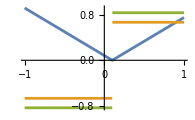

```mathematica
Plot[{Φ[0.1,0.8,x],Π[0.1,0.8,x],Ψ[0.1,0.8,x]},{x,-1,1}]
```

```mathematica
tmp=D[Π[x0,v,x],v]//FullSimplify
```

Sign[x-x0]/(2 (1-v^2)^(3/2))

```mathematica
tmp2=D[(2 HeavisideTheta[x-x0]-1)/(2 (1-v^2)^(3/2)),x]
```

DiracDelta[x-x0]/((1-v^2)^(3/2))

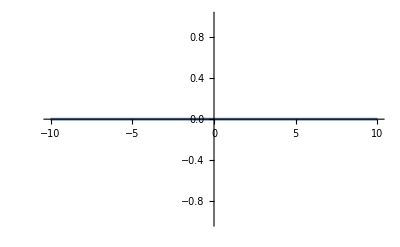

```mathematica
Plot[{DiracDelta[x-x0]/((1-v^2)^(3/2))(*-Sign[x-x0]/(2 (1-v^2)^(3/2))*)}/.{x0->1,v->0.9},{x,-10,10}]
```

```mathematica
rho[x_,x0_]=-q DiracDelta[x-x0];
```

```mathematica
dLdz = Ψ[x0,v,x]D[Ψ[x0,v,x],x0]+rho[x0,x] D[Φ[x0,v,x],x0]-Π[x0,v,x]D[Π[x0,v,x],x0]+Φ[x0,v,x]D[rho[x0,x],x0]//FullSimplify
```

(q DiracDelta[-x+x0] Sign[x-x0])/(2 √(1-v^2))-(q Abs[x-x0] DiracDelta'[-x+x0])/(2 √(1-v^2))-1/4 Sign[x-x0] Sign'[x-x0]

```mathematica
Integrate[dLdz,{x,-L,L}]
```

$Aborted

```mathematica
D[Ψ[x0,v,x],v]
```

(v Sign[x-x0])/(2 (1-v^2)^(3/2))

```mathematica
D[Π[x0,v,x],v]//FullSimplify
```

Sign[x-x0]/(2 (1-v^2)^(3/2))

```mathematica
dLdv = Ψ[x0,v,x]D[Ψ[x0,v,x],v]+rho[x0,x] D[Φ[x0,v,x],v]-Π[x0,v,x]D[Π[x0,v,x],v]+Φ[x0,v,x]D[rho[x0,x],v]//FullSimplify
```

-(q v Abs[x-x0] DiracDelta[-x+x0])/(2 (1-v^2)^(3/2))

```mathematica
Integrate[dLdv,{x,-L,L}]
```

0

```mathematica
dLidz=Ψr[x0,v,x]D[Ψ[x0,v,x],x0]-Πr[x0,v,x]D[Π[x0,v,x],x0]+Φr[x0,v,x]D[rho[x0,x],x0]//FullSimplify
```

-q Φr[x0,v,x] DiracDelta'[-x+x0]+((v Πr[x0,v,x]-Ψr[x0,v,x]) Sign'[x-x0])/(2 √(1-v^2))

```mathematica
Integrate[dLidz,{x,-L,L}]
```

$Aborted

```mathematica
dLidv=Ψr[z,v,x]D[Ψ[z,v,x],v]-Πr[z,v,x]D[Π[z,v,x],v]+Φr[z,v,x]D[rho[z,x],v]//FullSimplify
```

-(Sign[x-z] (Πr[z,v,x]-v Ψr[z,v,x]))/(2 (1-v^2)^(3/2))

```mathematica
Integrate[dLidv,{x,-L,L}]
```

$Aborted